```mathematica
RedBlueGreen6[key_]:=Block[{
red=Map[SymbolToLabel[#]&,ListofVars[allGraphs6[key,"colofourrealnull"]]]//Sort,
blue=Map[SymbolToLabel[#]&,ListofVars[allGraphs6[key,"colofour"]]]//Sort,
all=Map[SymbolToLabel[#]&,ListofVars[allGraphs6[0,"colofour"]]]//Sort,
green
},
green=all;
Table[green=Select[green,ToString[#]≠ToString[r]&],{r,red}];
Table[green=Select[green,ToString[#]≠ToString[b]&],{b,blue}];
green=Sort[green];
{red,blue,green}
]
```

```mathematica
RedBlueGreen[key_,allGraphs_]:=Block[{
red=Map[SymbolToLabel[#]&,ListofVars[allGraphs[key,"colofourrealnull"]]]//Sort,
blue=Map[SymbolToLabel[#]&,ListofVars[allGraphs[key,"colofour"]]]//Sort,
all=Map[SymbolToLabel[#]&,ListofVars[allGraphs[0,"colofour"]]]//Sort,
green
},
green=all;
Table[green=Select[green,ToString[#]≠ToString[r]&],{r,red}];
Table[green=Select[green,ToString[#]≠ToString[b]&],{b,blue}];
green=Sort[green];
{red,blue,green}
]
```

```mathematica
Tally[Table[Length[RedBlueGreen6[k][[3]]],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&]}]]//Sort
```

$Aborted

```mathematica
Table[allGraphs6[k,"graph"],{k,Select[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&],Length[RedBlueGreen6[#][[3]]]==6&]}]
```

$Aborted

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Table[allGraphs6[k,"graph"],{k,Select[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&],Length[RedBlueGreen6[#][[3]]]==0&]}]
```

```mathematica
{-Graphics-,-Graphics-}
```

```mathematica
Table[allGraphs6[k,"graph"],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&EdgeCount[allGraphs6[#,"graph"]]==2&]}]
```

```mathematica
Table[allGraphs6[k,"graph"],{k,Select[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&],Length[RedBlueGreen6[#][[3]]]==6&]}]
```

```mathematica
Table[allGraphs6[k,"graph"],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&EdgeCount[allGraphs6[#,"graph"]]==1&]}]
```

```mathematica
Table[allGraphs6[k,"graph"],{k,Select[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&],Length[RedBlueGreen6[#][[3]]]==3&]}]
```

```mathematica
Table[allGraphs6[k,"graph"],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&EdgeCount[allGraphs6[#,"graph"]]==3&]}]
```

```mathematica
Table[allGraphs6[k,"graph"],{k,Select[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&],Length[RedBlueGreen6[#][[3]]]==1&]}]
```

```mathematica
Table[allGraphs6[k,"graph"],{k,Select[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&],Length[RedBlueGreen6[#][[3]]]==0&]}]
```

```mathematica
Table[allGraphs6[k,"graph"],{k,Select[Keys[allGraphs6],Length[RedBlueGreen6[#][[3]]]==7&]}]
```

```mathematica
TableForm[Sort[Tally[Table[RedBlueGreen6[k][[3]],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&]}]],#1[[2]]#2[[2]]&],TableDepth->2]
```

```mathematica
vals346=Table[{Length[RedBlueGreen6[k][[3]]],Length[RedBlueGreen6[FindComplement[ k,allGraphs6]][[3]]]},{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&]}]
```

```mathematica
{{0,0},{14,4},{22,10},{26,19},{22,33},{23,31},{20,30},{13,31},{10,22},{4,14},{0,0},{4,14},{10,22},{4,14},{10,22},{19,26},{10,22},{4,14},{10,22},{14,26},{6,22},{14,26},{20,30},{14,26},{10,22},{4,14},{6,22},{19,26},{10,22},{14,26},{20,30},{13,31},{10,22},{14,26},{20,30},{14,26},{21,26},{23,31},{20,30},{14,26},{6,22},{4,14},{10,22},{14,26},{10,22},{19,26},{20,30},{14,26},{10,22},{13,31},{21,26},{14,26},{20,30},{23,31},{21,26},{14,26},{10,22},{14,26},{20,30},{13,31},{20,30},{23,31},{20,30},{19,26},{20,30},{23,31},{20,30},{23,31},{30,20},{31,23},{20,30},{19,26},{10,22},{4,14},{10,22},{14,26},{6,22},{14,26},{33,22},{19,26},{10,22},{19,26},{20,22},{9,26},{20,22},{23,23},{20,22},{14,26},{6,22},{9,26},{20,22},{9,26},{14,22},{31,23},{20,30},{14,26},{20,22},{23,23},{14,22},{23,17},{30,20},{23,23},{20,22},{9,26},{6,22},{14,26},{14,22},{9,26},{20,22},{31,23},{20,22},{14,26},{20,30},{23,17},{14,22},{23,23},{22,20},{23,17},{14,22},{9,26},{14,22},{17,23},{9,30},{17,23},{30,20},{23,23},{20,22},{23,23},{22,20},{17,23},{22,20},{26,19},{30,20},{23,23},{20,30},{14,26},{10,22},{4,14},{6,22},{19,26},{10,22},{14,26},{20,22},{14,26},{6,22},{9,26},{20,22},{9,26},{14,22},{31,23},{20,22},{19,26},{10,22},{9,26},{33,22},{19,26},{20,22},{23,23},{20,30},{14,26},{14,22},{31,23},{20,22},{23,17},{22,20},{23,23},{14,22},{9,26},{6,22},{9,26},{20,22},{14,26},{20,22},{17,23},{14,22},{9,26},{9,30},{23,17},{14,22},{17,23},{30,20},{23,17},{20,22},{14,26},{14,22},{31,23},{20,30},{23,23},{22,20},{23,23},{20,22},{17,23},{30,20},{23,23},{22,20},{31,13},{30,20},{23,31},{20,30},{13,31},{10,22},{14,26},{20,30},{14,26},{21,26},{31,23},{20,30},{14,26},{20,22},{23,23},{14,22},{23,17},{30,20},{23,23},{20,30},{14,26},{14,22},{31,23},{20,22},{23,17},{30,20},{23,31},{21,26},{23,17},{30,20},{23,17},{30,9},{26,14},{22,20},{17,23},{9,30},{9,26},{14,22},{17,23},{14,22},{23,17},{26,21},{17,23},{14,22},{17,23},{22,14},{16,16},{22,14},{26,14},{22,14},{17,23},{14,22},{16,16},{26,21},{17,23},{22,14},{26,14},{22,20},{23,17},{22,14},{26,14},{22,14},{26,9},{22,10},{26,19},{22,20},{23,23},{20,30},{14,26},{6,22},{4,14},{10,22},{14,26},{10,22},{19,26},{20,22},{9,26},{6,22},{14,26},{14,22},{9,26},{20,22},{23,23},{14,22},{9,26},{6,22},{9,26},{20,22},{14,26},{20,22},{17,23},{9,30},{9,26},{14,22},{17,23},{14,22},{23,17},{30,20},{31,23},{20,22},{9,26},{10,22},{19,26},{20,22},{19,26},{33,22},{23,23},{14,22},{14,26},{20,30},{23,17},{20,22},{31,23},{30,20},{23,17},{14,22},{14,26},{20,22},{23,23},{20,30},{31,23},{22,20},{17,23},{20,22},{23,23},{22,20},{23,23},{30,20},{26,14},{30,20},{23,31},{20,30},{14,26},{10,22},{13,31},{21,26},{14,26},{20,30},{31,23},{20,22},{14,26},{20,30},{23,17},{14,22},{23,23},{22,20},{17,23},{14,22},{9,26},{9,30},{23,17},{14,22},{17,23},{26,21},{17,23},{14,22},{17,23},{22,14},{16,16},{22,14},{31,13},{30,20},{23,23},{14,22},{14,26},{20,30},{23,17},{20,22},{31,23},{30,20},{23,17},{21,26},{23,31},{30,9},{23,17},{30,20},{26,14},{22,14},{16,16},{14,22},{17,23},{22,14},{17,23},{26,21},{26,14},{22,14},{23,17},{22,20},{26,9},{22,14},{26,14},{22,10},{26,14},{22,20},{23,31},{21,26},{14,26},{10,22},{14,26},{20,30},{13,31},{20,30},{23,17},{14,22},{9,26},{14,22},{17,23},{9,30},{17,23},{30,20},{23,17},{20,22},{14,26},{14,22},{31,23},{20,30},{23,23},{22,14},{17,23},{14,22},{16,16},{26,21},{17,23},{22,14},{26,14},{30,20},{23,17},{14,22},{14,26},{20,22},{23,23},{20,30},{31,23},{22,14},{16,16},{14,22},{17,23},{22,14},{17,23},{26,21},{31,13},{30,9},{23,17},{21,26},{23,17},{30,20},{23,31},{30,20},{26,9},{22,14},{23,17},{22,14},{26,14},{22,20},{26,14},{22,10},{26,19},{22,33},{23,31},{20,30},{19,26},{20,30},{23,31},{20,30},{23,31},{30,20},{23,23},{20,22},{23,23},{22,20},{17,23},{22,20},{26,19},{22,20},{23,23},{20,22},{17,23},{30,20},{23,23},{22,20},{26,14},{22,20},{23,17},{22,14},{26,14},{22,14},{26,9},{22,10},{26,19},{22,20},{17,23},{20,22},{23,23},{22,20},{23,23},{30,20},{26,14},{22,14},{23,17},{22,20},{26,9},{22,14},{26,14},{22,10},{26,9},{22,14},{23,17},{22,14},{26,14},{22,20},{26,14},{22,6},{26,9},{30,9},{26,9},{22,6},{26,9},{22,6},{14,4},{22,10},{26,19},{22,20},{17,23},{9,30},{9,26},{6,22},{4,14},{6,22},{9,26},{6,22},{9,26},{20,22},{14,26},{10,22},{14,26},{14,22},{9,26},{14,22},{17,23},{14,22},{14,26},{10,22},{9,26},{20,22},{14,26},{14,22},{23,23},{20,30},{19,26},{20,22},{23,23},{20,22},{23,17},{22,20},{17,23},{14,22},{9,26},{10,22},{14,26},{14,22},{14,26},{20,22},{23,23},{20,22},{19,26},{20,30},{23,17},{20,22},{23,23},{22,20},{23,17},{20,22},{19,26},{20,22},{23,23},{20,30},{23,23},{30,20},{31,23},{33,22},{31,23},{30,20},{31,23},{30,20},{26,14},{26,21},{17,23},{20,22},{14,26},{10,22},{14,26},{14,22},{9,26},{14,22},{31,23},{20,30},{13,31},{20,30},{17,23},{9,30},{17,23},{22,14},{23,17},{21,26},{14,26},{14,22},{23,17},{14,22},{16,16},{30,20},{23,31},{20,30},{23,23},{22,20},{17,23},{22,14},{26,14},{22,14},{23,17},{14,22},{14,26},{21,26},{16,16},{14,22},{23,17},{30,20},{23,23},{20,30},{23,31},{22,14},{17,23},{22,20},{26,9},{30,9},{23,17},{20,22},{23,17},{22,14},{17,23},{22,14},{31,13},{30,20},{31,23},{30,20},{26,14},{26,21},{26,14},{22,10},{26,14},{22,14},{17,23},{14,22},{14,26},{10,22},{9,26},{20,22},{14,26},{14,22},{23,17},{21,26},{14,26},{14,22},{23,17},{14,22},{16,16},{26,21},{17,23},{20,30},{13,31},{9,30},{31,23},{20,30},{17,23},{22,20},{23,31},{20,30},{17,23},{30,20},{23,23},{22,14},{26,9},{22,14},{16,16},{14,22},{14,26},{14,22},{23,17},{21,26},{23,17},{22,14},{23,17},{20,22},{17,23},{30,9},{23,17},{22,14},{26,14},{22,14},{23,23},{20,30},{17,23},{30,20},{23,31},{22,20},{26,14},{30,20},{31,23},{26,21},{31,13},{30,20},{26,14},{22,10},{26,14},{22,20},{23,23},{20,30},{19,26},{20,22},{23,23},{20,22},{23,17},{30,20},{23,31},{20,30},{23,23},{22,20},{17,23},{22,14},{26,14},{22,20},{23,31},{20,30},{17,23},{30,20},{23,23},{22,14},{26,19},{22,33},{23,31},{22,20},{26,19},{22,20},{26,9},{22,6},{26,9},{22,14},{17,23},{20,22},{23,17},{22,14},{23,17},{30,9},{26,14},{22,20},{23,23},{22,20},{26,9},{22,14},{26,9},{22,6},{26,9},{22,20},{23,23},{22,14},{26,14},{22,20},{26,9},{22,10},{26,19},{30,20},{26,14},{22,10},{26,14},{22,6},{14,4},{22,10},{26,9},{22,14},{17,23},{14,22},{9,26},{10,22},{14,26},{14,22},{14,26},{20,22},{23,17},{14,22},{14,26},{21,26},{16,16},{14,22},{23,17},{22,14},{16,16},{14,22},{14,26},{14,22},{23,17},{21,26},{23,17},{22,14},{17,23},{20,22},{23,17},{22,14},{23,17},{30,9},{26,14},{26,21},{17,23},{9,30},{13,31},{20,30},{17,23},{20,30},{31,23},{22,20},{17,23},{20,30},{23,31},{22,14},{23,23},{30,20},{26,14},{22,14},{17,23},{20,30},{23,23},{22,20},{23,31},{30,20},{26,14},{26,21},{31,23},{30,20},{26,14},{30,20},{31,13},{22,6},{26,14},{22,20},{23,23},{20,22},{19,26},{20,30},{23,17},{20,22},{23,23},{30,20},{23,23},{20,30},{23,31},{22,14},{17,23},{22,20},{26,9},{22,14},{23,17},{20,22},{17,23},{30,9},{23,17},{22,14},{26,14},{22,20},{23,23},{22,20},{26,9},{22,14},{26,9},{22,10},{26,14},{22,20},{17,23},{20,30},{23,31},{22,14},{23,23},{30,20},{26,19},{22,20},{23,31},{22,33},{26,9},{22,20},{26,19},{22,6},{26,9},{22,14},{23,23},{22,20},{26,9},{22,20},{26,14},{22,10},{26,14},{30,20},{26,19},{22,6},{26,14},{22,10},{14,4},{22,6},{26,9},{22,20},{23,17},{20,22},{19,26},{20,22},{23,23},{20,30},{23,23},{30,9},{23,17},{20,22},{23,17},{22,14},{17,23},{22,14},{26,14},{22,14},{23,23},{20,30},{17,23},{30,20},{23,31},{22,20},{26,9},{22,20},{23,23},{22,14},{26,14},{22,20},{26,9},{22,6},{26,14},{22,14},{17,23},{20,30},{23,23},{22,20},{23,31},{30,20},{26,9},{22,14},{23,23},{22,20},{26,9},{22,20},{26,14},{22,10},{26,9},{22,20},{23,31},{22,20},{26,19},{22,33},{26,19},{22,6},{26,14},{30,20},{26,14},{22,10},{26,19},{22,10},{14,4},{22,10},{26,19},{30,20},{31,23},{33,22},{31,23},{30,20},{31,23},{30,20},{31,13},{30,20},{31,23},{30,20},{26,14},{26,21},{26,14},{22,10},{26,14},{30,20},{31,23},{26,21},{31,13},{30,20},{26,14},{22,10},{26,19},{30,20},{26,14},{22,10},{26,14},{22,6},{14,4},{22,10},{26,14},{26,21},{31,23},{30,20},{26,14},{30,20},{31,13},{22,10},{26,14},{30,20},{26,19},{22,6},{26,14},{22,10},{14,4},{22,6},{26,14},{30,20},{26,14},{22,10},{26,19},{22,10},{14,4},{22,10},{31,13},{22,10},{14,4},{22,10},{14,4}}
```

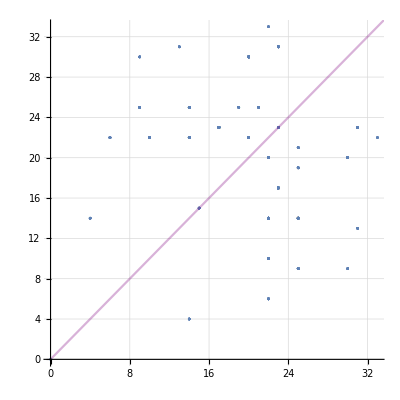

```mathematica
Show[ListPlot[vals346, AspectRatio->1, GridLines->Automatic],Plot[x,{x,0,40}, PlotStyle->Directive[Purple,Opacity[0.3]]]]
```

```mathematica
TableForm[Sort[Tally[Table[Length[RedBlueGreen6[k][[3]]],{k,Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&]}]]],TableDepth->2]
```

$Aborted

```mathematica
{{0, 2}, {4, 10}, {6, 16}, {9, 40}, {10, 30}, {13, 10}, {14, 130}, {16, 12}, {17, 60}, {19, 20}, {20, 120}, {21, 16}, {22, 170}, {23, 160}, {26, 126}, {30, 70}, {31, 40}, {33, 6}}
```

```mathematica
Table[Labeled[allGraphs6[k,"graph"],Style[k,Red]],{k,Select[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&],Length[RedBlueGreen6[#][[3]]]==33&]}]
```

```mathematica
{-Graphics-28764,-Graphics-27246,-Graphics-22708,-Graphics-9490,-Graphics-364}
```

```mathematica
7,33,
```

```mathematica
Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexCount[g]==6&&VertexDegree[g,1]==0&&EdgeCount[g]==10
]&]
```

{29524}

```mathematica
Length[RedBlueGreen6[29524][[3]]]
```

146

## The graphs with maximal green

```mathematica
Select[Keys[allGraphs2],With[{g=allGraphs2[#,"graph"]},VertexCount[g]==2&&VertexDegree[g,1]==0&&EdgeCount[g]==0
]&]
```

{0}

```mathematica
Length[RedBlueGreen[0,allGraphs2][[3]]]
```

0

```mathematica
Select[Keys[allGraphs3],With[{g=allGraphs3[#,"graph"]},VertexCount[g]==3&&VertexDegree[g,1]==0&&EdgeCount[g]==1
]&]
```

{1}

```mathematica
Length[RedBlueGreen[1,allGraphs3][[3]]]
```

1

```mathematica
Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4&&VertexDegree[g,1]==0&&EdgeCount[g]==3
]&]
```

{13}

```mathematica
Select[Keys[allGraphs4],With[{g=allGraphs4[#,"graph"]},VertexCount[g]==4&&VertexDegree[g,1]==0&&EdgeCount[g]==1
]&]
```

{9,3,1}

```mathematica
Length[RedBlueGreen[9,allGraphs4][[3]]]
```

4

```mathematica
Length[RedBlueGreen[13,allGraphs4][[3]]]
```

7

```mathematica
Select[Keys[allGraphs5],With[{g=allGraphs5[#,"graph"]},VertexCount[g]==5&&VertexDegree[g,1]==0&&EdgeCount[g]==6
]&]
```

{364}

```mathematica
Length[RedBlueGreen[364,allGraphs5][[3]]]
```

33

```mathematica
Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},VertexCount[g]==6&&VertexDegree[g,1]==0&&EdgeCount[g]==10
]&]
```

{29524}

```mathematica
Length[RedBlueGreen[29524,allGraphs6][[3]]]
```

146

## Seeing red, blue together

```mathematica
Map[Length,RedBlueGreen[13,allGraphs4]]//Total
```

0